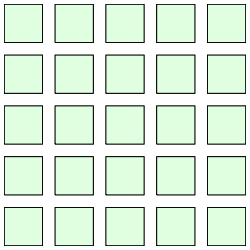

```mathematica
GraphicsGrid[Table[Graphics[{LightGreen,EdgeForm[Black],Rectangle[]},AspectRatio->RandomReal[{0,3}]],{5},{5}]]
```

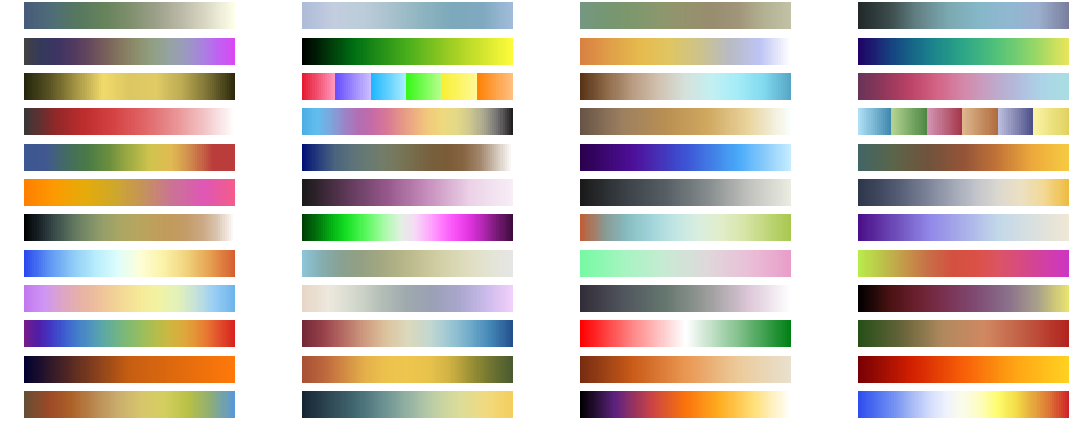

```mathematica
GraphicsGrid[Partition[ColorData[#,"Image"]&/@ColorData["Gradients"],4]]
```

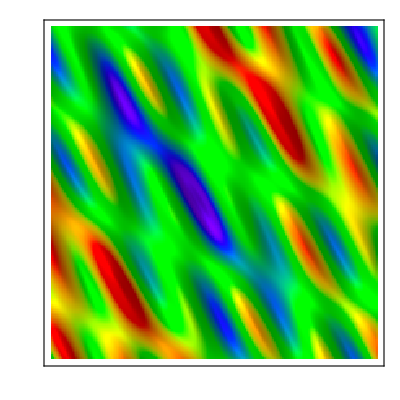

```mathematica
ReliefPlot[Table[Evaluate[Sum[30 Sin[RandomReal[4,2].{x,y}],{5}]],{x,0,10,.05},{y,0,10,.05}]+550,BoxRatios->{1,1,.4},ColorFunction->ColorData["VisibleSpectrum"],ColorFunctionScaling->False]
```

```mathematica
Import["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=1tf6","PDB",Background->Black]
```

-Graphics3D-

```mathematica
spiral[Graphics[g_,___],n_]:=Graphics[Table[Rotate[Translate[g,{k,0}/10],2 π k (2-GoldenRatio),{0,0}],{k,n}]]
```

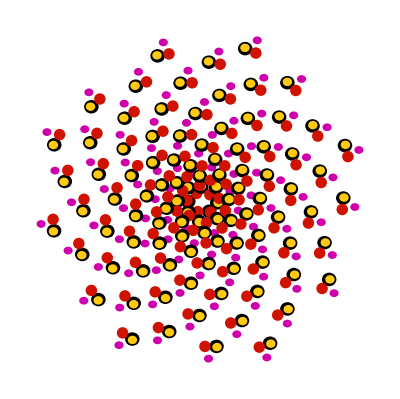

```mathematica
spiral[-Graphics-, 100]
```

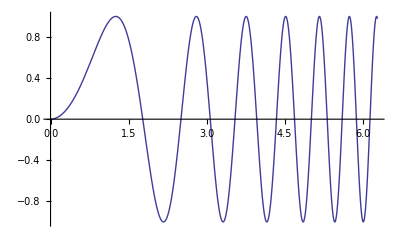
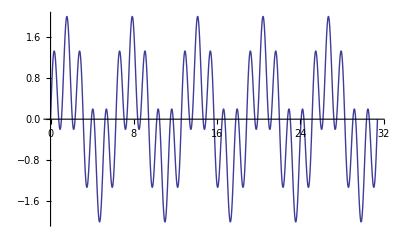
{-Graphics-,√(π/2) √(2/π) x,-Graphics-,-cos(x)-1/5 cos(5 x)}

```mathematica
{, ∫Sin[x^2] ⅆx, , ∫(Sin[x] + 
     Sin[5 x]) ⅆx}
```

```mathematica
Plot3D[Sin[x + Cos[y]], {x, -4, 4}, {y, -4, 4}, PlotStyle -> {0.6, Specularity[0.47058823529411764, ]}, Axes -> ]
```

-Graphics3D-

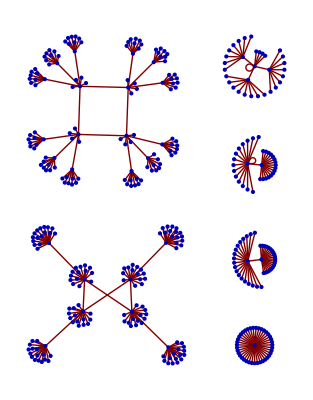

```mathematica
GraphPlot[Table[i->Mod[i^2,200],{i,400}]]
```

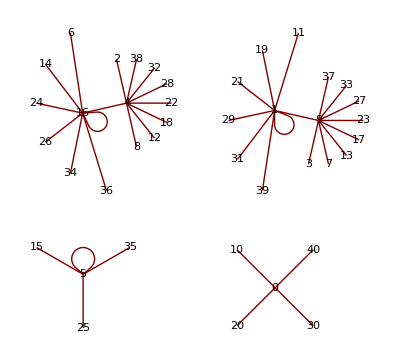

```mathematica
GraphPlot[Table[i->Mod[i^2,20],{i,40}],VertexLabeling->True]
```

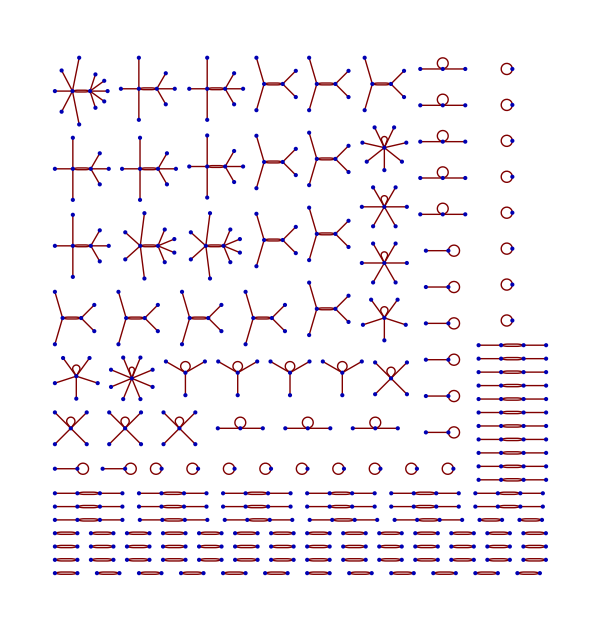

```mathematica
GraphPlot[Table[i->FromDigits[Reverse[IntegerDigits[i,2]],2],{i,0,511}]]
```

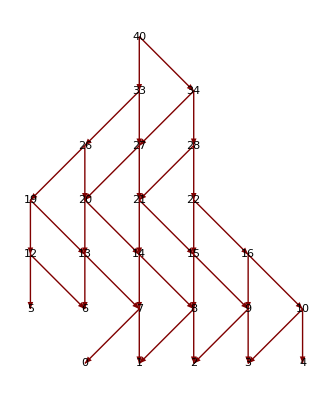

```mathematica
LayeredGraphPlot[Flatten[Thread/@Last[Reap[Module[{f},f[n_/;n<7]=1;
f[n_]:=f[n]=f[Sow[n-7,n]]+f[Sow[n-6,n]];f[40]],_,Rule]]],VertexLabeling->True]
```

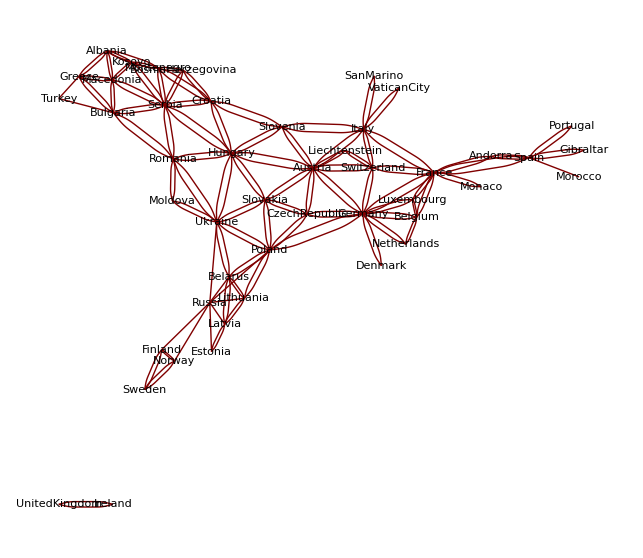

```mathematica
GraphPlot[Flatten[Thread[#->CountryData[#,"BorderingCountries"]]&/@CountryData["Europe"]],VertexLabeling->True]
```

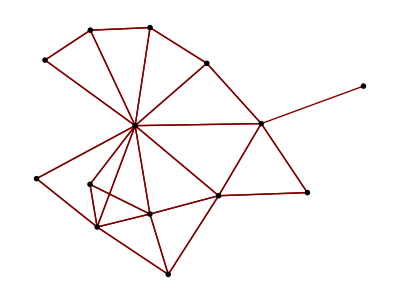

```mathematica
GraphPlot[Flatten[Thread[#->CountryData[#,"BorderingCountries"]]&/@CountryData["SouthAmerica"]],VertexRenderingFunction->(Inset[Show[CountryData[#2,"Shape"],ImageSize->30],#]&),MultiedgeStyle->None]
```

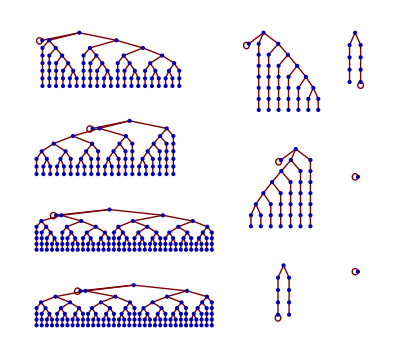

```mathematica
TreePlot[Table[i->FromDigits[RotateRight[IntegerDigits[i,2]],2],{i,0,511}]]
```

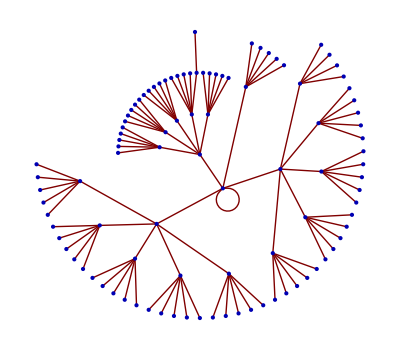

```mathematica
GraphPlot[Table[i->Mod[2^i,100],{i,100}]]
```

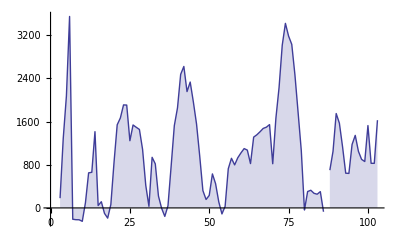

```mathematica
ListLinePlot[ElementData[#,"MeltingPoint"]&/@ElementData[],Filling->Axis]
```

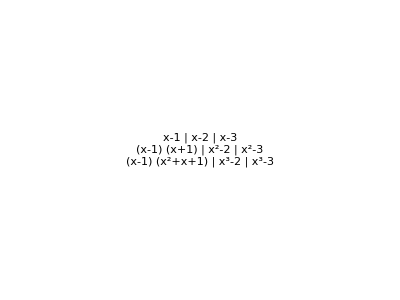

```mathematica
Graphics[Rotate[Text[Style[Grid[Table[Factor[x^i-j],{i,3},{j,3}],Frame->All],Large]],45 °]]
```